# Correlation matrices

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

DatedTrendDuration[datedprices]
DatedTrendDuration[dates, prices]
calculates TrendDuration with date info.

## Database

```mathematica
path = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","sp500v3.wdx"}];
database = Import[path];
```

```mathematica
database = SortBy[database,#["Sector"]&];
```

## Correlation matrix

```mathematica
GetPartitionedKey[database_,key_,partitionSize_,skip_]:=Transpose[Map[Partition[#[key],partitionSize,skip]&,database]];
GetPartitionedKey[database_,key_,partitionSize_,skip_,drop_]:=Transpose[Map[Partition[Drop[#[key],drop],partitionSize,skip]&,database]];
```

```mathematica
Middle[l_List /; Length[l]>1]:=Part[l,Floor[Length[l]/2]];
Middle[l_List /; Length[l]==1]:=First[l];
FirstLast[l_]:={First[l],Last[l]};

MarketStatePlot[corrMatrix_,date_:None]:=Block[{ticksHorizontal,ticksVertical},
ticksHorizontal = Map[{Middle[Last[#]],First[#]}&,Normal[PositionIndex[database[[All,"Sector"]]]]];
ticksVertical = MapAt[Column[Characters[#],Spacings->-0.2]&,ticksHorizontal,{All,2}];

MatrixPlot[
corrMatrix,
FrameTicks->{{ticksHorizontal[[1;;-1;;2]],None},{ticksVertical[[2;;-1;;2]],None}},
PlotTheme->"Monochrome",
Frame->True,
ColorFunction->ColorData["LightTemperatureMap"],
PlotRange->{-1,1},
PlotLabel->date,
ImageSize->800,
PlotLegends->Automatic
]
];
```

### Para precios

Crear partición de fechas y precios

```mathematica
temporalMarketMatrix = GetPartitionedKey[database,"Prices",100,10];
partitionedDates = GetPartitionedKey[database,"Dates",100,10];
```

Obtener matriz de correlación

```mathematica
corrMatrices = ProgressMap[Correlation[Transpose[#]]&,temporalMarketMatrix];
dateIntervals = Table[FirstLast[partitionedDates[[i,1]]],{i,1,Length[partitionedDates]}];
```

Graficar

```mathematica
plots = ProgressTable[MarketStatePlot[corrMatrices[[i]],dateIntervals[[i]]],{i,1,Length[corrMatrices]}];
```

```mathematica
Manipulate[Part[plots,i],{i,1,Length[plots],1}]
```

Part::partd: Part specification plots⟦1⟧ is longer than depth of object.

Eigenvalores

```mathematica
eigen = Map[Eigenvalues,corrMatrices];
```

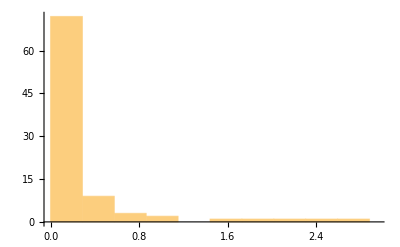

```mathematica
Histogram[Select[eigen[[3]],#>0.01&]]
```

Exportar

```mathematica
ExportImages[FileNameJoin[{NotebookDirectory[],"CorrelationMatrix","corr.png"}],plots]
```

### Para retornos

```mathematica
temporalMarketMatrix = GetPartitionedKey[database,"Returns",100,10];
partitionedDates = GetPartitionedKey[database,"Dates",100,10,1];
```

```mathematica
corrMatrices = ProgressMap[Correlation[Transpose[#]]&,temporalMarketMatrix];
dateIntervals = Table[FirstLast[partitionedDates[[i,1]]],{i,1,Length[partitionedDates]}];
```

```mathematica
plots = ProgressTable[MarketStatePlot[corrMatrices[[i]],dateIntervals[[i]]],{i,1,Length[corrMatrices]}];
```

```mathematica
ExportImages[FileNameJoin[{NotebookDirectory[],"CorrelationMatrix","corr.png"}],plots];
```

```mathematica
Manipulate[Part[plots,i],{i,1,Length[plots],1}]
```

### Record breaking

```mathematica
NewRecord[lastRecord_,list_]:=SelectFirst[list,#>lastRecord&];
GetRecords[list_]:=Block[{recordCanditates,records},
recordCanditates = DeleteDuplicates[list];
records = DeleteCases[Drop[FixedPointList[NewRecord[#,recordCanditates]&,0],1],_Missing];
Return[records];
];
Diff[prices_, lag_:1]:= If[Length[prices]≥ 2,
Drop[prices, lag] - Drop[prices, -lag],
Nothing
];
GetRecordTimes[list_]:=Diff[Flatten[Map[FirstPosition[list,#]&,GetRecords[list]]]];
GetNumberOfRecordBreaks[datedPrices_]:={Last[datedPrices[[All,1]]],Length[GetRecordTimes[TrendDuration[datedPrices[[All,2]]]]]};
```

```mathematica
DatedPrices[market_]:=Thread[{market["Dates"],market["Prices"]}];
DatedNumberOfRecordBreaks[market_Association, window_ , skip_ ]:=Block[{partDatedPrices},
partDatedPrices = Partition[DatedPrices[market],window,skip];
Map[GetNumberOfRecordBreaks,partDatedPrices]
];
```

```mathematica
recordBreakDatabase = ProgressTable[DatedNumberOfRecordBreaks[database[[i]],100,10],{i,1,Length[database]}];
```

```mathematica
RowCorrelation[row_,data_]:=Map[N@Correlation[data[[row]],#]&,data];
CorrMatrix[data_]:=Table[RowCorrelation[i,data],{i,1,Length[data],1}];
```

```mathematica
recordBreakValues = recordBreakDatabase[[All,All,2]];
```

```mathematica
Length[recordBreakValues]
```

404

```mathematica
partitioned = Map[Partition[#,50,1]&,recordBreakValues];
```

```mathematica
Length[partitioned[[1]]]
```

339

```mathematica
partitionedDates = GetPartitionedKey[database,"Dates",100,10];
dateIntervals = Table[FirstLast[partitionedDates[[i,1]]],{i,1,Length[partitionedDates]}];
```

```mathematica
recordBreakMatrixTimeSlices = Transpose[partitioned];
```

```mathematica
corrMatrices = ProgressParallelMap[CorrMatrix,recordBreakMatrixTimeSlices];
```

```mathematica
plots = ProgressTable[MarketStatePlot[corrMatrices[[i]],dateIntervals[[i]]],{i,1,Length[corrMatrices]}];
```

```mathematica
Manipulate[Part[plots,i],{i,1,Length[plots],1}]
```

```mathematica
ExportImages[FileNameJoin[{NotebookDirectory[],"CorrelationMatrix","corr.png"}],plots];
```

- Build databases of NASDAQ and Dow-Jones, DAX, Japan, India, etc. 
- Calculate record breaks for entire market in a non-overlaping window. A distribution for the entire market and see evolution in time.